# Bin Packing Project Revised Quang Vu

## Proposal state

This is an revised of the proposal function I changed many of variable names inspired by Sahib Khalsa, but the code is the same for both of us. This changed was made because I have the same idea of code but for some reason Mathematica was not happy with my variable with one character for example: b1,b2, i1,i2.

```mathematica
newstate[state_]:=Module[
(*local variables*)
{binchoice1,binchoice2,itemchange1,itemchange2,newstate=state},
(*Chooses 2 random indexes of the binassignment list and holds them as a new variable*)
binchoice1=RandomInteger[{1,n}];
binchoice2=RandomInteger[{1,n}];
(*Randomly (uniformly) select an item i1 from bin b1 and item i2 from bin b2*)
itemchange1=RandomInteger[{1,m}];
itemchange2=RandomInteger[{1,m}];
(*Print[itemchange1,itemchange2]*);

(*Assigns the new bin assignments corresponding the the indexes (binchoice) and making them the item change (new bin assignment)*)
newstate[[binchoice1]]=itemchange1;
newstate[[binchoice2]]=itemchange2;

(*returns the new binassignment*)
newstate
]
```

## Load Functions And Objective function

In this code section, I will define my load function and my objective function.

```mathematica
LoadMod[bin_,state_]:=Module[
{Load,Loadlist={}},(*an empty list to hold the loads of each bin*)
Do[
Load=Sum[If[bin[[i]]==j,1,0]*state[[i]],{i,1,n}]; (*Indicator function from the text. This will check and assigns value a new local variable called Load*)
AppendTo[Loadlist,Load] (*assigns the load to a list*)
,{j,1,m}]; 
(*returns the Loadlist for the bins*)
Loadlist
]
```

```mathematica
objectiveFunction[bin_,state_]:=Sum[(LoadMod[bin,state][[i]])^2,{i,1,m}]
```

```mathematica
Loadave[state_]:=1/m Sum[state[[i]],{i,1,n}]
```

## Simulated Annealing

In this code chunk,  I input the m bin, n item and the size of the item which is a list of integers. Then, like most simulated annealing algorithm, we need an objective functions. I use the objective function above.

```mathematica
findBin[size_,n_,m_,f_,maxIter_]:=Module[
(*local variables*)
{β=1,βinc=1.001,iterations,
propState,currState,
binassignment,(*bin assignment*)
items,(* genrate the items*)
avgLoad, (*computes the Average load just like the previos section.*)
stop,(* This will create our condition in the last if statement*)
ρ,Δf,
fVals={}(*create an empty list for the values of f*)
},
(*From Sahib idea I would like to count for the number of iterations that takes place before Success!*)
iterations=0;
(*generates our items list and our binassignment list*)

items=RandomInteger[{1,size},n];
Print["items:",items];
binassignment=RandomInteger[{1,m},n]; 
(* sets currstate as my initial binassignment*) 

currState=binassignment;
(*Computes Load that is dependent upon items to compare with objective function later*)

avgLoad=1/m*Sum[items[[i]],{i,1,n}];

(*this is for stopping condition in our if statment later on*)
stop=m*avgLoad^2;
Do[
(*iterations to count the steps taken to reach bin loads(adapted from Sahib)*)
iterations+=1;

(* select a proposed next state which produces new bin based on newstate module*)
propState=newstate[currState];

(* select the next β in the annealing schedule *)
β*=βinc;

(* compute the acceptance ratio *) 
Δf=f[propState,items]-f[currState,items];
ρ=Exp[-β*Δf];

(* decide whether to accept the proposed transition *) 
If[RandomReal[]<ρ,
currState=propState
];
(* if a partition has been found, then quit *)
AppendTo[fVals,f[currState,items]];
If[f[currState,items]-stop==0,Print["Success!"];Break[] ]
,maxIter];

(* return values *) 
{β,fVals[[-1]],currState,iterations}
]
```

```mathematica
size=1;
n=100;
m=5;
maxIter=1000;
findBin[size,n,m,objectiveFunction,maxIter]
```

items:{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Success!

{1.08541,2000,{3,3,5,3,5,4,4,1,1,3,1,5,2,1,2,5,3,2,3,1,1,3,3,5,3,5,4,5,2,4,5,5,5,4,5,4,1,5,2,4,1,2,2,4,2,1,4,4,2,1,4,4,3,2,3,1,3,5,1,1,1,5,5,3,2,3,4,4,1,2,5,1,2,3,2,5,3,4,1,4,5,4,5,3,1,2,4,2,3,2,2,5,3,2,1,2,1,4,3,4},82}

It seems like the code is now running more perfectly compare to the original code.

## Discussion

First, we will discuss the effectiveness of simulated annealing for solving the bin packing problem. For this, I am just going to experiment with different values of bins and item such that we have an idea of how many times we have success.

```mathematica
size=3;
n=15;
m=3;
maxIter=1000;
findBin[size,n,m,objectiveFunction,maxIter]
```

items:{2,3,3,2,2,2,3,3,2,1,2,1,1,3,1}

{2.71692,321,{1,2,3,1,3,2,3,1,3,2,1,1,2,2,3},1000}

```mathematica
size=3;
n=100;
m=3;
maxIter=1000;
findBin[size,n,m,objectiveFunction,maxIter]
```

items:{2,3,1,1,3,3,1,2,1,1,3,3,2,1,3,2,2,3,1,3,3,1,3,3,3,2,2,1,2,3,1,2,2,1,3,2,1,1,3,3,2,2,2,1,3,2,2,3,2,2,3,2,1,2,3,2,2,3,3,3,2,2,1,2,2,1,2,3,2,2,1,1,1,1,1,2,1,3,1,3,1,1,2,3,3,2,3,3,2,1,3,1,3,3,3,3,3,3,3,3}

{2.71692,14841,{2,2,2,1,2,2,1,3,1,3,3,3,1,2,3,2,1,1,1,1,2,3,1,1,2,1,2,3,3,1,2,1,3,2,3,3,2,1,1,2,2,3,3,3,1,2,2,3,3,1,2,2,1,1,3,2,2,3,3,3,1,1,3,2,3,1,1,2,1,1,1,3,2,2,3,1,1,2,1,3,2,2,1,3,1,3,3,2,2,1,1,3,3,3,3,2,2,1,2,1},1000}

With odd number of bins and odd number of items size we seems to have pretty quick success!!!! Now, I will try with bigger odd and odd.

```mathematica
size=5;
n=50;
m=5;
maxIter=1000;
findBin[size,n,m,objectiveFunction,maxIter]
```

items:{1,5,3,1,2,2,4,2,1,2,4,5,1,3,4,4,2,1,2,3,1,5,5,1,3,5,3,2,2,5,1,4,5,4,3,1,3,4,3,5,2,1,2,4,1,5,4,2,2,3}

{2.71692,4091,{1,5,2,3,5,4,2,2,5,1,4,5,1,3,2,1,5,5,5,4,3,4,3,2,4,2,2,1,2,2,5,4,1,1,4,3,3,3,5,4,5,1,1,5,1,3,1,3,1,3},1000}

```mathematica
(*size=5;
n=100;
m=5;
maxIter=10000;
findBin[size,n,m,objectiveFunction,maxIter])*
```

After some computation I can find the packing for n=5 and 5 as our item size after running for couple of time. I note down that I have ran this for 15 times.

```mathematica
(*size=5;
n=100;
m=5;
maxIter=30000;
findBin[size,n,m,objectiveFunction,maxIter]*)
```

Note that with the code chunk above, I have turn our iterations into 30,000 and we still have not found a perfect bin packing for 5 if I ran it one time.

Lets test out m= odd and even item size

```mathematica
(*size=3;
n=200;
m=6;
maxIter=1000;
findBin[size,n,m,objectiveFunction,maxIter]*)
```

Seems like an odd number of size and an even number of bins will still able to produce a good bin packing for a decent amount of iterations and does not loss in precision in computation.

```mathematica
(*size=4;
n=200;
m=4;
maxIter=10000;
findBin[size,n,m,objectiveFunction,maxIter]*)
```

Before I was testing with 1000 and after many iterations I loss count I still can not get a bin packing.  Hence, I increase to 10,000 iterations we can get a good packing for an even items and even bins situation.

```mathematica
(*size=6;
n=200;
m=6;
maxIter=30000;
findBin[size,n,m,objectiveFunction,maxIter]*)
```

With 30000 iterations, I can not even find a good bin packing with item size of six and six bins.

## Optimal Packing Iterations

In the next section, I will modify my simulated annealing to print our iterations some optimal packing when we hit one. The modification is easy I just changed my output.

```mathematica
findBin2[size_,n_,m_,f_,maxIter_]:=Module[
{β=1,βinc=1.001,
iterations,
propState,
currState,
binassignment,
items,
avgLoad,
stop,
ρ,Δf,fVals={}},
iterations=0;
items=RandomInteger[{1,size},n];
binassignment=RandomInteger[{1,m},n];
currState=binassignment;
avgLoad=1/m Sum[items[[i]],{i,1,n}];
stop=m*avgLoad^2;
Do[iterations+=1;
propState=newstate[currState];
β*=βinc;
Δf=f[propState,items]-f[currState,items];
ρ=Exp[-β*Δf];
If[RandomReal[]<ρ,currState=propState];
AppendTo[fVals,f[currState,items]];
If[f[currState,items]-stop==0,(*I just adding this part so that whenever the *)
Print["Success!"];
Break[]],maxIter];
iterations](*This code print our the optimal solution and the amount to get to the optimal solution *)
```

```mathematica
size=1;
n=100;
m=5;
maxIter=1000;
findBin2[size,n,m,objectiveFunction,maxIter]
```

Success!

25

Seems like the code is working

```mathematica
size=3;
n=100;
m=3;
maxIter=10000;
findBin2[size,n,m,objectiveFunction,maxIter]
```

General::munfl: Exp[-821.948] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-826.703] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-713.446] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
size=3;
n=200;
m=3;
maxIter=10000;
findBin2[size,n,m,objectiveFunction,maxIter]
```

Success!

6

```mathematica
size=3;
n=300;
m=3;
maxIter=20000;
findBin2[size,n,m,objectiveFunction,maxIter]
```

General::munfl: Exp[-911.986] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-787.978] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1031.29] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

10000

From the code chunks above it seems like we have found a good packing for three bins with items size of three and we generating 200 items. From all of our output, we can say that with larger amount of items no matter what the size is, the code definitely take more time to solve the bin packing problem. In other word, it ‘s harder to find a good packing for larger number of items.

## Further work

When we reflect on our previous find_bin function, we could modify it in such a way that it only generates bins where the sum of the items is divisible by the number of bins. This is important because if we don’t have a bin sum that’s divisible by the number of bins, we can’t pack evenly. In other words, we would either end up with an empty bin or one bin that has a different sum than the others. This is not ideal for achieving a balanced distribution of items across the bins. This new code chunk will print our the amount of iterations until we have a good packing as well, but I have remove the print success when we reach a good packing for a later idea I have in mind.

```mathematica
findBin3[size_,n_,m_,f_,maxIter_]:=Module[{β=1,βinc=1.001,iterations,success=0,propState,currState,binassignment,items,avgLoad,sumitems,stop,ρ,Δf,fVals={},optimalSolution},iterations=0;
Do[items=RandomInteger[{1,size},n];
sumitems=Sum[items[[i]],{i,1,n}];
If[IntegerQ[sumitems/m],items;Break[]],maxIter];
binassignment=RandomInteger[{1,m},n];
currState=binassignment;
avgLoad=1/m*Sum[items[[i]],{i,1,n}];
stop=m*avgLoad^2;
Do[iterations+=1;
propState=newstate[currState];
β*=βinc;
Δf=f[propState,items]-f[currState,items];
ρ=Exp[-β*Δf];
If[RandomReal[]<ρ,currState=propState];
AppendTo[fVals,f[currState,items]];
If[f[currState,items]-stop==0,success=1;Break[]],maxIter];
(*return values*){iterations,success}]
```

```mathematica
size=5;
n=100;
m=5;
maxIter=1000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{429,1}

```mathematica
size=5;
n=600;
m=5;
maxIter=10000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{611,1}

```mathematica
size=5;
n=700;
m=5;
maxIter=30000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

General::munfl: Exp[-1158.72] is too small to represent as a normalized machine number; precision may be lost.

{471,1}

## Explore the effectiveness of simulated annealing for solving the bin packing problem. How close can you get to an optimal solution? How many iterations of the simulated annealing does this require? How does this depend on N and M?

I have created this loop module so I can run the findbin 3 multiple times in a row and have a list of the amount of iteration. Then from there, we can potentially plot the

```mathematica
loopfindbin[size_,n_,m_,objectiveFunction_,maxIter_, number_]:=Module [
{list={}, times},
Do[times= findBin3[size,n,m,objectiveFunction,maxIter];
AppendTo[list, times]
,number];
list
]
size=5;
n=100;
m=5;
maxIter=1000;
list= loopfindbin[size,n,m,objectiveFunction,maxIter, 10]
```

{{378,1},{124,1},{885,1},{423,1},{723,1},{150,1},{957,1},{208,1},{540,1},{692,1}}

```mathematica
{{71,1},{269,1},{518,1},{104,1},{467,1},{297,1},{480,1},{652,1},{122,1},{174,1}}
list2 = Table[list[[n,1]],{n,1,10}]
```

{{71,1},{269,1},{518,1},{104,1},{467,1},{297,1},{480,1},{652,1},{122,1},{174,1}}

{148,355,615,193,77,92,594,292,188,128}

```mathematica
Mean[list2]//N
```

268.2

```mathematica
size=6;
n=100;
m=6;
maxIter=100000;
list= loopfindbin[size,n,m,objectiveFunction,maxIter, 20]//Quiet
```

{{1627,1},{356,1},{1391,1},{583,1},{842,1},{1093,1},{848,1},{296,1},{560,1},{1277,1},{2327,1},{1514,1},{822,1},{556,1},{1494,1},{426,1},{896,1},{1189,1},{132,1},{362,1}}

```mathematica
list2 = Table[list[[n,1]],{n,1,20}]
```

{1627,356,1391,583,842,1093,848,296,560,1277,2327,1514,822,556,1494,426,896,1189,132,362}

```mathematica
Mean[list2]//N
```

929.55

```mathematica
size=6;
n=120;
m=6;
maxIter=100000;
list120item= loopfindbin[size,n,m,objectiveFunction,maxIter, 20]//Quiet
```

{{1767,1},{512,1},{292,1},{823,1},{1390,1},{2839,1},{500,1},{768,1},{206,1},{1106,1},{618,1},{239,1},{255,1},{2012,1},{945,1},{471,1},{555,1},{1033,1},{173,1},{764,1}}

```mathematica
meanlist120item = Table[list120item[[n,1]],{n,1,20}]
```

{1767,512,292,823,1390,2839,500,768,206,1106,618,239,255,2012,945,471,555,1033,173,764}

```mathematica
Mean[meanlist120item]//N
```

863.4

```mathematica
size=6;
n=190;
m=6;
maxIter=100000;
list190item= loopfindbin[size,n,m,objectiveFunction,maxIter, 20]//Quiet
meanlist190item = Table[list190item[[n,1]],{n,1,20}] 
Mean[meanlist190item]//N
```

{{1736,1},{523,1},{874,1},{455,1},{591,1},{731,1},{872,1},{835,1},{818,1},{1242,1},{1586,1},{345,1},{919,1},{3228,1},{307,1},{235,1},{1514,1},{705,1},{572,1},{770,1}}

{1736,523,874,455,591,731,872,835,818,1242,1586,345,919,3228,307,235,1514,705,572,770}

942.9

```mathematica
size=6;
n=200;
m=6;
maxIter=100000;
list200item= loopfindbin[size,n,m,objectiveFunction,maxIter, 20]//Quiet
meanlist200item = Table[list200item[[n,1]],{n,1,20}] 
Mean[meanlist200item]//N
```

{{646,1},{3828,1},{994,1},{747,1},{797,1},{397,1},{1048,1},{929,1},{659,1},{1922,1},{482,1},{917,1},{611,1},{398,1},{1036,1},{877,1},{1188,1},{1053,1},{239,1},{220,1}}

{646,3828,994,747,797,397,1048,929,659,1922,482,917,611,398,1036,877,1188,1053,239,220}

949.4

```mathematica
size=6;
n=250;
m=6;
maxIter=100000;
list250item= loopfindbin[size,n,m,objectiveFunction,maxIter, 20]//Quiet
meanlist250item = Table[list250item[[n,1]],{n,1,20}] 
Mean[meanlist250item]//N
```

{{271,1},{399,1},{489,1},{405,1},{223,1},{3668,1},{260,1},{819,1},{434,1},{368,1},{1436,1},{720,1},{202,1},{527,1},{1284,1},{269,1},{733,1},{211,1},{792,1},{559,1}}

{271,399,489,405,223,3668,260,819,434,368,1436,720,202,527,1284,269,733,211,792,559}

703.45

```mathematica
size=6;
n=300;
m=6;
maxIter=100000;
list300item= loopfindbin[size,n,m,objectiveFunction,maxIter, 20]//Quiet
meanlist300item = Table[list300item[[n,1]],{n,1,20}] 
Mean[meanlist300item]//N
```

{{739,1},{330,1},{426,1},{574,1},{832,1},{1083,1},{1541,1},{735,1},{819,1},{779,1},{2244,1},{2280,1},{1060,1},{404,1},{1169,1},{1060,1},{771,1},{481,1},{2699,1},{745,1}}

{739,330,426,574,832,1083,1541,735,819,779,2244,2280,1060,404,1169,1060,771,481,2699,745}

1038.55

```mathematica
nvalues= {120,190, 200, 250, 300}
meanlistplot={863.4, 942.9,949.4,802.2 ,1038.55}
plotData=Transpose[{nvalues,meanlistplot}]
```

{120,190,200,250,300}

{863.4,942.9,949.4,802.2,1038.55}

{{120,863.4},{190,942.9},{200,949.4},{250,802.2},{300,1038.55}}

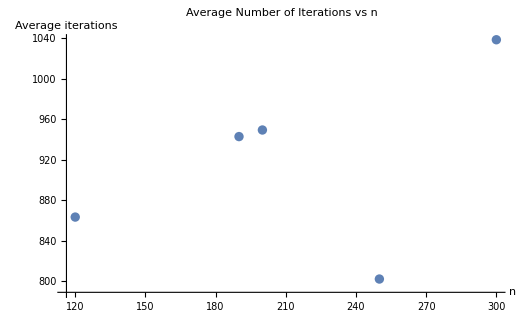

```mathematica
(*Create the plot*)
ListPlot[plotData,AxesLabel->{"n","Average iterations"},PlotLabel->"Average Number of Iterations vs n"]
```

I have created this loop module so I can run the “findbin 3” multiple times in a row and have a list of the amount of iteration. Then from there, we can potentially plot the

```mathematica
calculateMeanIterations[size_,n_,m_,objectiveFunction_,maxIter_,numtry_]:=Module[
{list,meanlist},
list=loopfindbin[size,n,m,objectiveFunction,maxIter,numtry]//Quiet;
meanlist=Table[list[[i,1]],{i,1,numtry}];

Mean[meanlist]//N]
```

```mathematica
size=1;
n=2;
m=5;
maxIter=10;
numtry=20;
calculateMeanIterations[size,n,m,objectiveFunction,maxIter,numtry]
```

10.

```mathematica
size=1;
m=2;
maxIter=100;
numtry=40;
Do[n=i;
meanIterations=calculateMeanIterations[size,n,m,objectiveFunction,maxIter,numtry];
Print["For n = ",n,", the mean number of iterations is ",meanIterations],
{i,100,300,10}]
```

For n = 100, the mean number of iterations is 12.825

For n = 110, the mean number of iterations is 11.675

For n = 120, the mean number of iterations is 11.35

For n = 130, the mean number of iterations is 10.6

For n = 140, the mean number of iterations is 13.4

For n = 150, the mean number of iterations is 12.7

For n = 160, the mean number of iterations is 15.675

For n = 170, the mean number of iterations is 12.9

For n = 180, the mean number of iterations is 13.275

For n = 190, the mean number of iterations is 15.

For n = 200, the mean number of iterations is 16.425

For n = 210, the mean number of iterations is 17.85

For n = 220, the mean number of iterations is 16.375

For n = 230, the mean number of iterations is 18.2

For n = 240, the mean number of iterations is 15.925

For n = 250, the mean number of iterations is 15.25

For n = 260, the mean number of iterations is 19.525

For n = 270, the mean number of iterations is 16.2

For n = 280, the mean number of iterations is 16.7

For n = 290, the mean number of iterations is 17.95

For n = 300, the mean number of iterations is 18.525

I want to improve this by making an empty list, and  then put each inter to their respective n items with the mean amount amount of iterations.

```mathematica
size=1;
m=2;
maxIter=100;
numtry=40;
nvalues= Range[100,300,10];
meanlistplot={};
Do[n=i;
meanIterations=calculateMeanIterations[size,n,m,objectiveFunction,maxIter,numtry];
Print["For n = ",n,", the mean number of iterations is ",meanIterations];
If[MemberQ[nvalues,n],AppendTo[meanlistplot,meanIterations]],{i,100,300,10}]
plotData=Transpose[{nvalues,meanlistplot}]
```

For n = 100, the mean number of iterations is 10.625

For n = 110, the mean number of iterations is 10.875

For n = 120, the mean number of iterations is 11.625

For n = 130, the mean number of iterations is 12.425

For n = 140, the mean number of iterations is 13.4

For n = 150, the mean number of iterations is 12.075

For n = 160, the mean number of iterations is 12.95

For n = 170, the mean number of iterations is 15.125

For n = 180, the mean number of iterations is 15.875

For n = 190, the mean number of iterations is 14.825

For n = 200, the mean number of iterations is 14.575

For n = 210, the mean number of iterations is 16.35

For n = 220, the mean number of iterations is 19.375

For n = 230, the mean number of iterations is 14.2

For n = 240, the mean number of iterations is 19.025

For n = 250, the mean number of iterations is 20.75

For n = 260, the mean number of iterations is 18.775

For n = 270, the mean number of iterations is 15.275

For n = 280, the mean number of iterations is 20.05

For n = 290, the mean number of iterations is 15.05

For n = 300, the mean number of iterations is 19.525

{{100,10.625},{110,10.875},{120,11.625},{130,12.425},{140,13.4},{150,12.075},{160,12.95},{170,15.125},{180,15.875},{190,14.825},{200,14.575},{210,16.35},{220,19.375},{230,14.2},{240,19.025},{250,20.75},{260,18.775},{270,15.275},{280,20.05},{290,15.05},{300,19.525}}

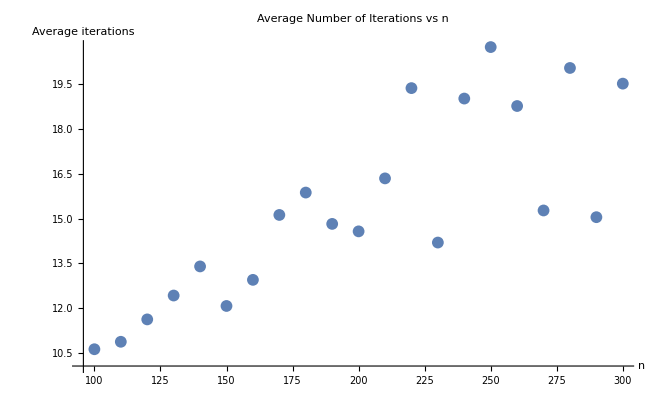

```mathematica
ListPlot[plotData,AxesLabel->{"n","Average iterations"},PlotLabel->"Average Number of Iterations vs n"]
```

We see that with more items we are required more iterations on average to reach the optimal packing. Even though, there might be cases that the algorithm get lucky and find the optimal solution faster.

```mathematica
size=3;
m=2;
maxIter=100000;
numtry=40;
nvalues= Range[10,300,20];
meanlistplot={};
Do[n=i;
meanIterations=calculateMeanIterations[size,n,m,objectiveFunction,maxIter,numtry];
Print["For n = ",n,", the mean number of iterations is ",meanIterations];
If[MemberQ[nvalues,n],AppendTo[meanlistplot,meanIterations]],{i,10,300,10}]
plotData=Transpose[{nvalues,meanlistplot}]
```

For n = 10, the mean number of iterations is 9.025

For n = 20, the mean number of iterations is 10.15

For n = 30, the mean number of iterations is 11.55

For n = 40, the mean number of iterations is 13.6

For n = 50, the mean number of iterations is 14.15

For n = 60, the mean number of iterations is 14.05

For n = 70, the mean number of iterations is 12.625

For n = 80, the mean number of iterations is 12.6

For n = 90, the mean number of iterations is 17.675

For n = 100, the mean number of iterations is 17.175

For n = 110, the mean number of iterations is 13.85

For n = 120, the mean number of iterations is 14.475

For n = 130, the mean number of iterations is 19.95

For n = 140, the mean number of iterations is 16.

For n = 150, the mean number of iterations is 17.575

For n = 160, the mean number of iterations is 20.85

For n = 170, the mean number of iterations is 16.725

For n = 180, the mean number of iterations is 17.95

For n = 190, the mean number of iterations is 20.675

For n = 200, the mean number of iterations is 21.3

For n = 210, the mean number of iterations is 20.475

For n = 220, the mean number of iterations is 21.125

For n = 230, the mean number of iterations is 20.35

For n = 240, the mean number of iterations is 23.775

For n = 250, the mean number of iterations is 25.125

For n = 260, the mean number of iterations is 25.4

For n = 270, the mean number of iterations is 21.025

For n = 280, the mean number of iterations is 23.2

For n = 290, the mean number of iterations is 22.55

For n = 300, the mean number of iterations is 24.4

{{10,9.025},{30,11.55},{50,14.15},{70,12.625},{90,17.675},{110,13.85},{130,19.95},{150,17.575},{170,16.725},{190,20.675},{210,20.475},{230,20.35},{250,25.125},{270,21.025},{290,22.55}}

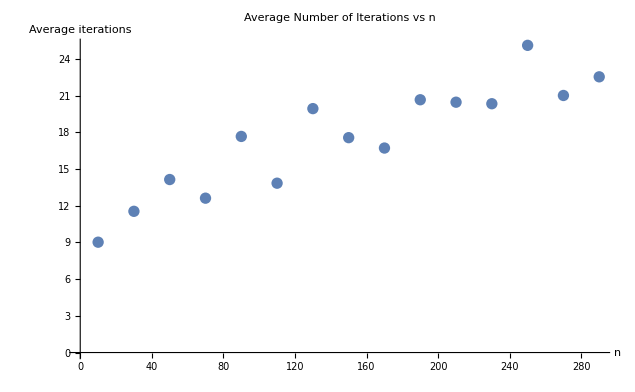

```mathematica
ListPlot[plotData,AxesLabel->{"n","Average iterations"},PlotLabel->"Average Number of Iterations vs n"]
```

```mathematica
size=2;
m=5;
maxIter=100000;
numtry=40;
nvalues= Range[5,100,5];
meanlistplot={};
Do[n=i;
meanIterations=calculateMeanIterations[size,n,m,objectiveFunction,maxIter,numtry];
Print["For n = ",n,", the mean number of iterations is ",meanIterations];
If[MemberQ[nvalues,n],AppendTo[meanlistplot,meanIterations]],{i,5,100,5}]
plotData=Transpose[{nvalues,meanlistplot}]
```

For n = 5, the mean number of iterations is 14.725

For n = 10, the mean number of iterations is 98.275

For n = 15, the mean number of iterations is 181.35

For n = 20, the mean number of iterations is 184.475

For n = 25, the mean number of iterations is 145.625

For n = 30, the mean number of iterations is 120.75

For n = 35, the mean number of iterations is 111.075

For n = 40, the mean number of iterations is 153.95

For n = 45, the mean number of iterations is 138.025

For n = 50, the mean number of iterations is 145.575

For n = 55, the mean number of iterations is 120.25

For n = 60, the mean number of iterations is 127.55

For n = 65, the mean number of iterations is 147.8

For n = 70, the mean number of iterations is 114.45

For n = 75, the mean number of iterations is 139.65

For n = 80, the mean number of iterations is 119.2

For n = 85, the mean number of iterations is 142.825

For n = 90, the mean number of iterations is 132.725

For n = 95, the mean number of iterations is 136.35

For n = 100, the mean number of iterations is 153.175

{{5,14.725},{10,98.275},{15,181.35},{20,184.475},{25,145.625},{30,120.75},{35,111.075},{40,153.95},{45,138.025},{50,145.575},{55,120.25},{60,127.55},{65,147.8},{70,114.45},{75,139.65},{80,119.2},{85,142.825},{90,132.725},{95,136.35},{100,153.175}}

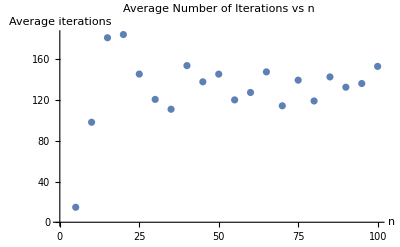

```mathematica
ListPlot[plotData,AxesLabel->{"n","Average iterations"},PlotLabel->"Average Number of Iterations vs n"]
```

The  trend for the previous one is not that good, but generaly,  it’s increasing

```mathematica
size=2;
m=5;
maxIter=100000;
numtry=40;
nvalues= Range[50,200,10];
meanlistplot={};
Do[n=i;
meanIterations=calculateMeanIterations[size,n,m,objectiveFunction,maxIter,numtry];
Print["For n = ",n,", the mean number of iterations is ",meanIterations];
If[MemberQ[nvalues,n],AppendTo[meanlistplot,meanIterations]],{i,50,200,10}]
plotData1=Transpose[{nvalues,meanlistplot}]
```

For n = 50, the mean number of iterations is 144.3

For n = 60, the mean number of iterations is 123.8

For n = 70, the mean number of iterations is 150.575

For n = 80, the mean number of iterations is 129.05

For n = 90, the mean number of iterations is 120.6

For n = 100, the mean number of iterations is 122.175

For n = 110, the mean number of iterations is 154.925

For n = 120, the mean number of iterations is 163.725

For n = 130, the mean number of iterations is 109.3

For n = 140, the mean number of iterations is 128.1

For n = 150, the mean number of iterations is 143.25

For n = 160, the mean number of iterations is 131.

For n = 170, the mean number of iterations is 170.15

For n = 180, the mean number of iterations is 142.075

For n = 190, the mean number of iterations is 151.675

For n = 200, the mean number of iterations is 143.375

{{50,144.3},{60,123.8},{70,150.575},{80,129.05},{90,120.6},{100,122.175},{110,154.925},{120,163.725},{130,109.3},{140,128.1},{150,143.25},{160,131.},{170,170.15},{180,142.075},{190,151.675},{200,143.375}}

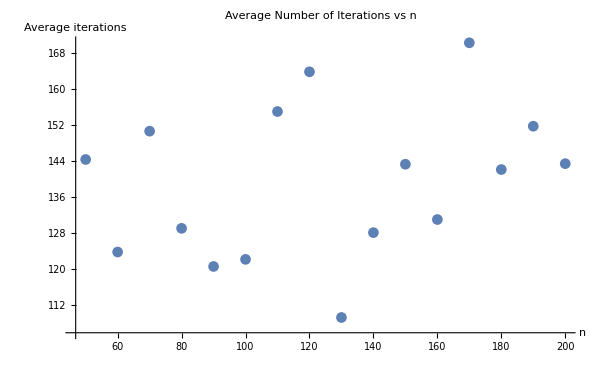

```mathematica
ListPlot[plotData1,AxesLabel->{"n","Average iterations"},PlotLabel->"Average Number of Iterations vs n"]
```

For n = 5, the mean number of iterations is 97501.5

For n = 10, the mean number of iterations is 50153.

For n = 15, the mean number of iterations is 3072.78

For n = 20, the mean number of iterations is 460.775

For n = 25, the mean number of iterations is 407.6

For n = 30, the mean number of iterations is 378.025

For n = 35, the mean number of iterations is 283.5

For n = 40, the mean number of iterations is 198.025

For n = 45, the mean number of iterations is 269.6

For n = 50, the mean number of iterations is 262.725

For n = 55, the mean number of iterations is 324.925

For n = 60, the mean number of iterations is 288.825

For n = 65, the mean number of iterations is 324.25

For n = 70, the mean number of iterations is 278.875

For n = 75, the mean number of iterations is 253.925

For n = 80, the mean number of iterations is 327.3

For n = 85, the mean number of iterations is 311.1

For n = 90, the mean number of iterations is 258.375

For n = 95, the mean number of iterations is 296.5

For n = 100, the mean number of iterations is 328.325

{{5,97501.5},{10,50153.},{15,3072.78},{20,460.775},{25,407.6},{30,378.025},{35,283.5},{40,198.025},{45,269.6},{50,262.725},{55,324.925},{60,288.825},{65,324.25},{70,278.875},{75,253.925},{80,327.3},{85,311.1},{90,258.375},{95,296.5},{100,328.325}}

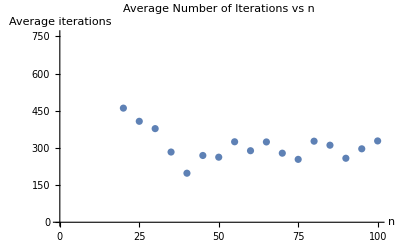

```mathematica
size=4;
m=5;
maxIter=100000;
numtry=40;
nvalues= Range[5,100,5];
meanlistplot={};
Do[n=i;
meanIterations=calculateMeanIterations[size,n,m,objectiveFunction,maxIter,numtry];
Print["For n = ",n,", the mean number of iterations is ",meanIterations];
If[MemberQ[nvalues,n],AppendTo[meanlistplot,meanIterations]],{i,5,100,5}]
plotData2=Transpose[{nvalues,meanlistplot}]
ListPlot[plotData2,AxesLabel->{"n","Average iterations"},PlotLabel->"Average Number of Iterations vs n"]
```

Our calculation initialy seem to be progress well, with an increasing trend observed in the iterations. However, our simulated annealing process has a probabilistic component. This means there’s a possibility that we might achieve optimal bin packing after fewer iterations.

Later in this project, I present evidence that a higher number of items significantly increases the iteration time. Interestingly, some larger numbers still manage to reach optimal bin packing quicker than others. This could be because certain numbers simplify the packing process.

We also observe that the computation time for smaller numbers is significantly less than for larger numbers. This insight could be crucial for optimizing our bin packing algorithm.

After reading some more papers about bin packing project, I realized that if n equal to really specific harmonic series number we will have really clean packing with many different bins of  6,24,65,184,469,1243,3231.
The set of number that the author of the paper mentioned is the following:  a(n) = k implies that there exists a set S of positive integers such that , max(S) = k and no set S’ exists with the same sum and a smaller maximal element. 
In other word, we consider the following set of a(n) = min{max S | S is a subset of n }
Here is a specific example for the sequence that we are looking at: 
When a(1) = 1, S = { 1 }, 
When a(2) = 2, S ={6}. To be more specifc, the set S = { 1, 2, 3, 6 } gives a 1/1 + 1/2 +1/3 1/4 = 2; exhaustive search shows that no set with a smaller maximal element can sum to 2, therefore a(2) = 6.
When a(3) = 24, S = { 1 2 3 4 5 6 8 9 10 15 18 20 24 }
When a(4) = 65, S = { 1 2 3 4 5 6 7 8 9 10 11 12 13 14 15 16 18 20 22 24 26 27 28 30 33 35 36 40 42 45 48 52 54 56 60 63 65 }
Cited: Greg Martin and Yue Shi, An algorithm for Egyptian fraction representations with restricted denominators, arXiv:2107.05076 [math.NT], 2021.
Lets start this hypothesis out!!! Since from previous observations we have really good packing efficiency form an odd number of bins and odd number size. We will continue to do this

```mathematica
size=5;
n=24;
m=5;
maxIter=10000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{1022,1}

```mathematica
size=5;
n=65;
m=5;
maxIter=10000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{393,1}

```mathematica
size=5;
n=184;
m=5;
maxIter=10000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{215,1}

```mathematica
size=5;
n=469;
m=5;
maxIter=30000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{378,1}

```mathematica
size=5;
n=1243;
m=5;
maxIter=30000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{257,1}

```mathematica
size=5;
n=3231;
m=5;
maxIter=30000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{230,1}

```mathematica
size=7;
n=3231;
m=7;
maxIter=30000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{629,1}

```mathematica
size=11;
n= 184;
m=11;
maxIter=50000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{13311,1}

We can see that this is really interesting because from the previous section, we have found out that with higher amount of item. Our simulated annealing will struggle to find a good bin packing. But that is not inherently true, our simulated annealing actually work quite sufficient, we should look into the mathematics  behind the bin packing. If we look for example n=65, we will have elements that will help to remove the excess in some of the bins like 21,39,44,and 55. This is a hand wavy proof that I have no clue how to make it rigorous.
I will try an even and even configuration to make sure this set of number truly work s well with he bin packing problems

```mathematica
size=4;
n= 65;
m=4;
maxIter=10000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{240,1}

```mathematica
size=4;
n= 1243;
m=4;
maxIter=10000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{85,1}

```mathematica
size=4;
n= 3231;
m=4;
maxIter=30000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

General::munfl: Exp[-998.991] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-940.689] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-783.012] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{252,1}

```mathematica
size=6;
n= 65;
m=6;
maxIter=30000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{990,1}

```mathematica
size=6;
n= 3231;
m=6;
maxIter=50000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{618,1}

Surprisingly, with the series form the set of specific number if the item sise is even and the number of even is actually have better efficiency than the previous case.

```mathematica
size=12;
n= 184;
m=12;
maxIter=50000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

The code  actually able to test this with 12 bins after 34 776 iterations.

## Graveyard

```mathematica
loopfindbin[size_,n_,m_,objectiveFunction_,maxIter_, number_]:=Module [
{list={}, times},
Do[times= findBin3[size,n,m,objectiveFunction,maxIter];
AppendTo[list, times]
,number];
list
]
```

```mathematica
size=5;
n=100;
m=5;
maxIter=10000;
findBin3[size,n,m,objectiveFunction,maxIter]
```

{130,1}

```mathematica
size=5;
n=100;
m=5;
maxIter=10000;
list= loopfindbin[size,n,m,objectiveFunction,maxIter, 50]//Quiet
```

{{384,1},{741,1},{614,1},{1097,1},{157,1},{1319,1},{652,1},{459,1},{784,1},{1155,1},{248,1},{171,1},{274,1},{500,1},{46,1},{394,1},{402,1},{480,1},{172,1},{257,1},{605,1},{299,1},{140,1},{204,1},{452,1},{294,1},{209,1},{213,1},{412,1},{568,1},{681,1},{1390,1},{208,1},{128,1},{438,1},{240,1},{70,1},{448,1},{199,1},{139,1},{351,1},{78,1},{571,1},{108,1},{729,1},{191,1},{99,1},{194,1},{109,1},{1156,1}}

Part::partw: Part 3 of {{384,384,384,384,384,384,384,384,384,384},{384,384,384,384,384,384,384,384,384,384}} does not exist.

{{384,384,384,384,384,384,384,384,384,384},{384,384,384,384,384,384,384,384,384,384}}⟦3,1⟧

```mathematica
list2= Table[list[[n,1]],{n,1,2}]
```

{384,384}

```mathematica
Mean[list]//N
```

{424.58,1.}

```mathematica
size=5;
m=5;
maxIter=10000;
nValues=Range[10,100,10]; (*Change this to the range of n values with steps for plotting convineance*)
list=Table[loopfindbin[size,n,m,objectiveFunction,maxIter,10],{n,nValues}];
```

```mathematica
list= Table[list[[n,1]],{n,1,10}]
```

{{{409,1},{10000,0},{10000,0},{10000,0},{10000,0},{10000,0},{10000,0},{783,1},{694,1},{258,1}},{{265,1},{154,1},{561,1},{133,1},{350,1},{2431,1},{505,1},{92,1},{531,1},{476,1}},{{975,1},{218,1},{2091,1},{84,1},{130,1},{166,1},{494,1},{1164,1},{313,1},{794,1}},{{101,1},{59,1},{151,1},{106,1},{105,1},{234,1},{85,1},{206,1},{339,1},{519,1}},{{857,1},{64,1},{144,1},{501,1},{167,1},{192,1},{811,1},{627,1},{251,1},{459,1}},{{132,1},{179,1},{223,1},{158,1},{645,1},{545,1},{158,1},{126,1},{228,1},{458,1}},{{861,1},{643,1},{923,1},{105,1},{1026,1},{491,1},{584,1},{240,1},{64,1},{177,1}},{{502,1},{776,1},{239,1},{458,1},{175,1},{130,1},{370,1},{335,1},{275,1},{830,1}},{{113,1},{152,1},{964,1},{624,1},{281,1},{856,1},{547,1},{112,1},{637,1},{215,1}},{{119,1},{667,1},{781,1},{841,1},{687,1},{203,1},{393,1},{146,1},{118,1},{425,1}}}

```mathematica
Mean[list]//N
```

{{409,1},{265,1},{975,1},{101,1},{857,1},{132,1},{861,1},{502,1},{113,1},{119,1}}

```mathematica
plotData =Transpose[{nValues,successfulIterations}]
```

{{10,{409,1}},{20,{265,1}},{30,{975,1}},{40,{101,1}},{50,{857,1}},{60,{132,1}},{70,{861,1}},{80,{502,1}},{90,{113,1}},{100,{119,1}}}

```mathematica
(*Calculate the average number of iterations for each n*)

averageIterations=Map[Mean,successfulIterations]

(*Create pairs of (n,average iterations) for plotting*)
plotData=Transpose[{nValues,averageIterations}];

(*Create the plot*)
ListPlot[plotData,AxesLabel->{"n","Average iterations"},PlotLabel->"Average Number of Iterations vs n"]
```

$Aborted